# Learning tabular data

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
?neurallogic`*
```

## Get data

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],
"PurchasePrice"->encoders["PurchasePrice"],
"MaintenanceCost"->encoders["MaintenanceCost"],
"Doors"->encoders["Doors"],
"Passengers"->encoders["Passengers"],
"Cargo"->encoders["Cargo"],
"Safety"->encoders["Safety"]
];
```

## Create net

```mathematica
{softNet,hardNet}=Block[{numClasses=Length[classes],classificationLayerSize},
classificationLayerSize=128*numClasses;
HardNeuralChain[{
HardNeuralMajority[inputSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

```mathematica
NetFlatten[trainableNet]
```

NetGraph[<>]

## Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
BatchSize->Automatic,
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
trainedSoftNet=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[result["TrainedNet"]],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
];
```

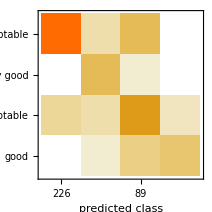
Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (90.51.6) %
Accuracy baseline | (68.82.5) %
Geometric mean of probabilities | 0.66 ± 0.056
Mean cross entropy | 0.415 ± 0.085
Single evaluation time | 4.12 ms/example
Batch evaluation speed | 2.46 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[trainedSoftNet,testData->"Acceptability"]
```

```mathematica
trainedSoftNet2=HardNetTransformWeights[trainedSoftNet,(If[#>0.5,1,0]&)/@#&]
```

NetGraph[<>]

```mathematica
measurements=ClassifierMeasurements[trainedSoftNet2,testData->"Acceptability"]
```

Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (90.51.6) %
Accuracy baseline | (68.82.5) %
Geometric mean of probabilities | 0.66 ± 0.056
Mean cross entropy | 0.415 ± 0.085
Single evaluation time | 3.87 ms/example
Batch evaluation speed | 2.8 examples/ms
-Graphics- |

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
```

```mathematica
hncwt=HardNetClassify[hnf,featureLayer,NetDecoder[encoders["Acceptability"]],testData,"Acceptability"];
eval=HardNetClassifyEvaluation[hncwt]
```

```mathematica
hncwt2=Association[{"Prediction"->trainedSoftNet2[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
eval2=HardNetClassifyEvaluation[hncwt2]
```

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

1.375 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize];
```

## Train standard net

```mathematica
classifier=Classify[trainData->"Acceptability",Method->"NeuralNetwork",PerformanceGoal->"Memory"]
```

ClassifierFunction[…]

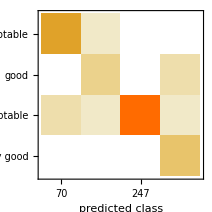
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 346
Accuracy | (98.00.8) %
Accuracy baseline | (72.52.4) %
Geometric mean of probabilities | 0.931 ± 0.017
Mean cross entropy | 0.0714 ± 0.018
Single evaluation time | 5.82 ms/example
Batch evaluation speed | 1.47 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData->"Acceptability"]
```

```mathematica
Information[classifier,"FunctionMemory"]
```

357. kB

## Notes

```mathematica
softWeights=Flatten[ExtractWeights[trainedSoftNet]];
```

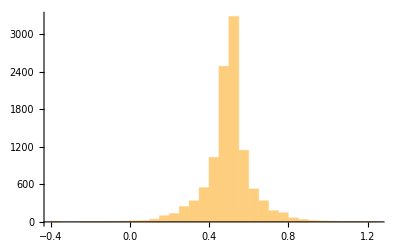

```mathematica
Histogram[softWeights,PlotRange->All]
```